## Constants

```mathematica
a0SI=5.291772108*10^-11;
hSI=6.6260693 *10^-34;
hbarSI=1/(2π)6.6260693 *10^-34;
a0=1;
hbar=1;
kB=1.3806504*10^-23;
me=9.10938215*10^-31;
mK=39.96399867;
mLi=6.0151223;
mRb=86.90918;
mNa=22.9897;
u=1.660538782*10^-27;
Eh=4.35974394*10^-18;
```

From tiemann's paper
C6=1.1793*10^7 cm^-1 A^6
in atomic units:

```mathematica
C6Na23K40=(hSI 1.1793*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6
C6Na23K40low=(hSI (1.1793-0.0120)*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6
C6Na23K40high=(hSI (1.1793+0.0120)*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6
```

2448.69

2423.77

2473.61

```mathematica
μ=(mNa*mK)/(mNa+mK)*u/me;
```

## potential definition

```mathematica
C6=C6Na23K40;
```

```mathematica
V[L_,r_]=-C6/r^6+L(L+1)*hbar^2/(2μ r^2);
Vlow[L_,r_]=-C6Na23K40low/r^6+L(L+1)*hbar^2/(2μ r^2);
Vhigh[L_,r_]=-C6Na23K40high/r^6+L(L+1)*hbar^2/(2μ r^2);
```

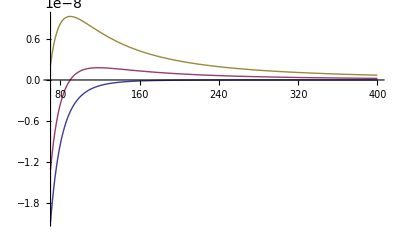

```mathematica
Plot[{V[0,r],V[1,r],V[2,r]},{r,70,400},PlotRange->All]
```

```mathematica
ain=18*a0;
```

## get the p-wave bound state from the s-wave

we calculate the accumulated phase at ain based on a binding energy of 148 MHz

```mathematica
aBoundary=400;
ES=-148*10^6;
DacPh=0;
acPh=1;

En=ES*hSI/Eh;
aBoundary=300;
solutionSwave=NDSolve[{psi''[r]==-(2μ)/hbar^2(En-V[0,r])*psi[r],psi[aBoundary]==acPh,psi'[aBoundary]==DacPh},psi,{r,ain,aBoundary},MaxSteps->500000,PrecisionGoal->11];
DacPh=psi'[ain]/.solutionSwave[[1]];
acPh=psi[ain]/.solutionSwave[[1]];
```

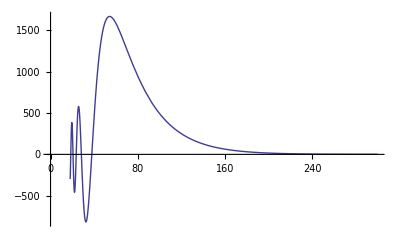

```mathematica
pl1=Plot[psi[r]/.solutionSwave,{r,ain,aBoundary},PlotRange->{{0,aBoundary},All}]
```

now use this accumulated phase to obtain the p-wave bound state by iteratively changing the energy ontil the wavefunction is decayed properly to zero at a certain distance.

```mathematica
aBoundary=400;

En=ES*hSI/Eh;          (*initial guess is s-wave bound state*)
dE=10*10^6*hSI/Eh;           (*initial stepsize *)

this=0;
aBoundary=400;
While[Abs[dE/(10^-3*hSI/Eh)]>1,
solutionPwave=NDSolve[{psi''[r]==-(2μ)/hbar^2(En-V[1,r])*psi[r],psi[ain]==acPh,psi'[ain]==DacPh},psi,{r,ain,aBoundary},MaxSteps->500000,PrecisionGoal->11];
prev=this;
this=(psi[aBoundary]/.solutionPwave)[[1]];
If[this*prev<0,dE=-0.5*dE];

En=En+dE;
];
Print["s-wave at:",ES*10^-6," MHz gives p-wave bound state at En=",En/(10^6*hSI/Eh)];
```

s-wave at:-148 MHz gives p-wave bound state at En=-71.6298

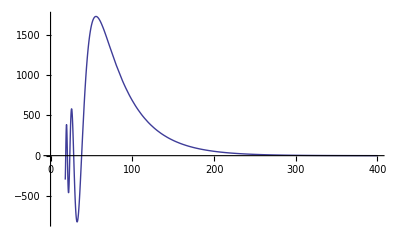

```mathematica
pl1=Plot[{psi[r]/.solutionPwave},{r,ain,aBoundary},PlotRange->{{0,aBoundary},All}]
```

## get the bound state from the scattering length

```mathematica
ascat=69*a0;  (*tiemann*)
```

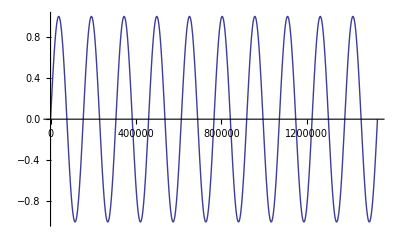

```mathematica
En=(10 kB)/(10^9 Eh);
Nosc=10;
KKK=SetPrecision[(√(2 μ En))/hbar,12];
Plot[Sin[KKK r],{r,0,(Nosc (2 π))/KKK}]
```

apply the scattering length as boundary condition and integrate inwards in two steps

```mathematica
aBoundary=Nosc(2π)/KKK+ascat;
DacPh=1;
acPh=0;

solution1=NDSolve[{psi''[r]==-(2μ)/hbar^2(En-V[0,r])*psi[r],psi[aBoundary]==acPh,psi'[aBoundary]==DacPh},psi,{r,ain,aBoundary},MaxSteps->500000,PrecisionGoal->11];
```

-4.77691

4.72501

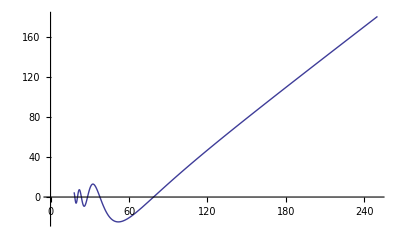

```mathematica
DacPh=psi'[ain]/.solution1[[1]]
acPh=psi[ain]/.solution1[[1]]
pl1=Plot[psi[r]/.solution1,{r,ain,250},PlotRange->{{0,250},All}]
```

now use this accumulated phase to obtain the bound state by iteratively changing the energy ontil the wavefunction is decayed properly to zero at a certain distance.

```mathematica
aBoundary=400;

En=-1*10^6*hSI/Eh;          (*initial guess is -1 MHz*)
dE=-10*10^6*hSI/Eh;           (*initial stepsize *)

this=0;
l=0;

While[Abs[dE/(10^-3*hSI/Eh)]>1,
solution1=NDSolve[{psi''[r]==-(2μ)/hbar^2(En-V[1,r])*psi[r],psi[ain]==acPh,psi'[ain]==DacPh},psi,{r,ain,aBoundary},MaxSteps->500000,PrecisionGoal->11];
prev=this;
this=(psi[aBoundary]/.solution1)[[1]];
If[this*prev<0,dE=-0.5*dE];

En=En+dE;
];
Print["bound state at En=",En/(10^6*hSI/Eh)];
```

bound state at En=-72.003

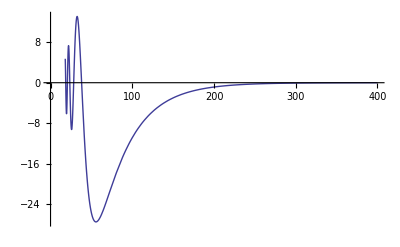

```mathematica
pl1=Plot[psi[r]/.solution1,{r,ain,aBoundary},PlotRange->{{0,400},All}]
```

## get the s-wave bound state from scattering length

```mathematica
ascat=-830*a0;  (*tiemann*)
```

```mathematica
ain=10*a0;
```

```mathematica
(2μ)/hbar^2
```

53207.3

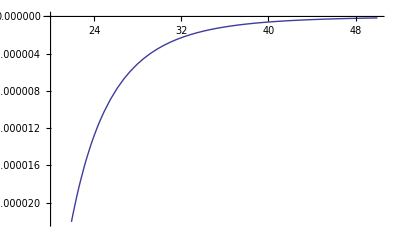

```mathematica
Plot[V[0,r],{r,20,50}]
```

```mathematica
En=(10 kB)/(10^9 Eh);
Nosc=10;
KKK=SetPrecision[(√(2 μ En))/hbar,12];
Plot[Sin[KKK r],{r,0,(Nosc (2 π))/KKK}]
```

3.16682×10^-14

-Graphics-

apply the scattering length as boundary condition and integrate inwards in two steps

```mathematica
aBoundary=Nosc(2π)/KKK+ascat;
DacPh=1;
acPh=0;

solution1=NDSolve[{psi''[r]==-(2μ)/hbar^2(En-V[0,r])*psi[r],psi[aBoundary]==acPh,psi'[aBoundary]==DacPh},psi,{r,ain,aBoundary},MaxSteps->500000,PrecisionGoal->11];
```

-230.545

30.1909

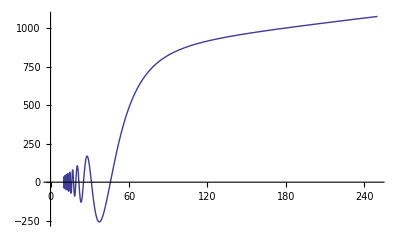

```mathematica
DacPh=psi'[ain]/.solution1[[1]]
acPh=psi[ain]/.solution1[[1]]
pl1=Plot[psi[r]/.solution1,{r,ain,250},PlotRange->{{0,250},All}]
```

now use this accumulated phase to obtain the bound state by iteratively changing the energy ontil the wavefunction is decayed properly to zero at a certain distance.

```mathematica
aBoundary=400;

En=-1*10^6*hSI/Eh;          (*initial guess is -1 MHz*)
dE=-10*10^6*hSI/Eh;           (*initial stepsize *)

this=0;
l=0;

While[Abs[dE/(10^-3*hSI/Eh)]>1,
solution1=NDSolve[{psi''[r]==-(2μ)/hbar^2(En-V[0,r])*psi[r],psi[ain]==acPh,psi'[ain]==DacPh},psi,{r,ain,aBoundary},MaxSteps->500000,PrecisionGoal->11];
prev=this;
this=(psi[aBoundary]/.solution1)[[1]];
If[this*prev<0,dE=-0.5*dE];

En=En+dE;
];
Print["bound state at En=",En/(10^6*hSI/Eh)];
```

bound state at En=-1630.12

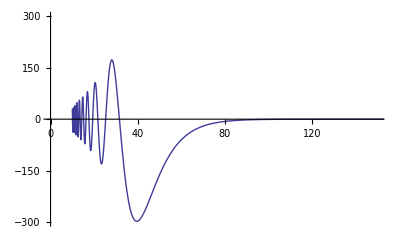

```mathematica
pl1=Plot[psi[r]/.solution1,{r,ain,aBoundary},PlotRange->{{0,150},{-300,300}}]
```